# Q9

hyperbola

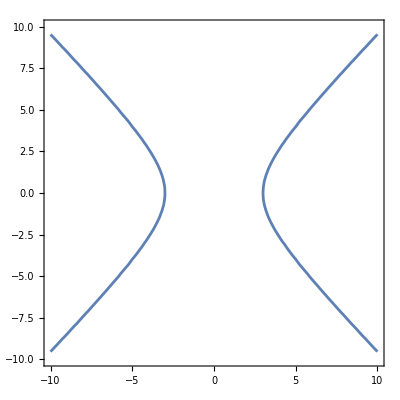

√2

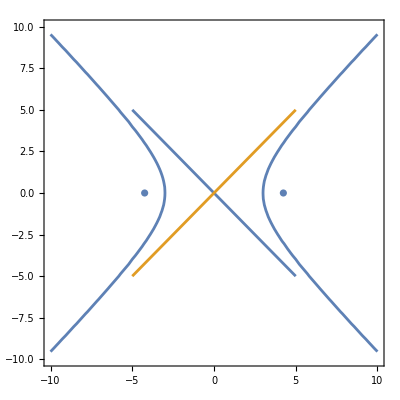

Ellipse

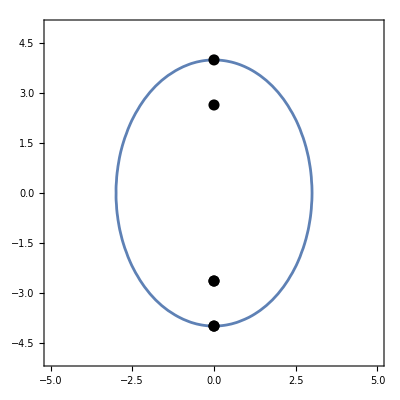

```mathematica
(*a*)
f[x_,y_]:=x^2-y^2-4x+8y-21
If[0^2-4*1*(-1)>0,
Print["hyperbola"],
Print["Not hyperbola"]
]
Solve[{D[f[x,y],x]==0,D[f[x,y],y]==0},{x,y}];
f[x+2,y+4]//Simplify;
g1=ContourPlot[f[x+2,y+4]==0,{x,-10,10},{y,-10,10}]
e=Sqrt[1+9/9]
foci1={e*3,0};
foci2 = {-e*3,0};
vertices = {{3,0},{-3,0}};
g2=ContourPlot[{y+x==0,y-x==0},{x,-5,5},{y,-5,5}];
p1=ListPlot[{foci1,foci2,vertices}];
Show[g1,g2,p1]
(*b*)
Clear[f]
f[x_,y_]:=16 x^2+9 y^2-64x-54y+1
If[0^2-4*16*9<0,
Print["Ellipse"],
Print["Not Ellipse"]
]
Solve[{D[f[x,y],x]==0,D[f[x,y],y]==0},{x,y}];
f[x+2,y+3]//Simplify;
g[x_,y_]:=16 x^2+9 y^2-144
g3=ContourPlot[g[x,y]==0,{x,-5,5},{y,-5,5}];
e=Sqrt[1-9/16];
foci={{0,4*e},{0,-4*e}};
vertices = {{0,4},{0,-4}};
p2=ListPlot[
{foci,vertices},
PlotStyle->{{Black,PointSize[0.02]}}
];
Show[g3,p2]
```